# Congruent Polygons

### Author

Eric W. Weisstein
August 31, 2026

This notebook downloaded from https://mathworld.wolfram.com/notebooks/PlaneGeometry/CongruentPolygons.nb.

For more information, see Eric's MathWorld entry https://mathworld.wolfram.com/CongruentPolygons.html.

©2026 Wolfram Research, Inc.

## Figure

Two congruent polygons related by a rigid motion.

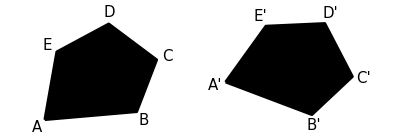

```mathematica
With[
	{
		p = {{0.5, 0.4}, {2.8, 0.6}, {3.3, 1.9}, {2.1, 2.8}, {0.8, 2.1}},
		q = RotationTransform[-Pi/7][#] + {4.4, 1.2} & ,
		ink = LightDarkSwitched[RGBColor[0.217, 0.217, 0.217], RGBColor[0.867, 0.867, 0.867]],
		fill = LightDarkSwitched[RGBColor[0.8, 0.87, 0.98], RGBColor[0.25, 0.38, 0.62]]
	},
	With[
		{
			labelPoints = Function[vertices,
				MapThread[
					Function[{vertex, previous, next},
						vertex - 0.28 Normalize[Normalize[previous - vertex] + Normalize[next - vertex]]
					],
					{vertices, RotateRight[vertices], RotateLeft[vertices]}
				]
			]
		},
		Graphics[
			{
				EdgeForm[Directive[ink, AbsoluteThickness[2]]],
				FaceForm[fill],
				Polygon[p],
				Polygon[q /@ p],
				MapThread[
					Text[Style[#1, ink, Italic, FontFamily -> "Times", 15], #2] & ,
					{{"A", "B", "C", "D", "E"}, labelPoints[p]}
				],
				MapThread[
					Text[Style[#1, ink, Italic, FontFamily -> "Times", 15], #2] & ,
					{{"A'", "B'", "C'", "D'", "E'"}, labelPoints[q /@ p]}
				]
			}
		]
	]
]
```